```mathematica
NormalizeData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
PortfolioChart[stocks_,start_,end_]:=Module[{s,mean,data,symbols,std,return},
s=NormalizeData[#,start,end]&/@stocks;
mean=Transpose@{s[[1]][[All,1]],Mean/@Transpose@(#[[All,2]]&/@s)};
data=s~Join~{mean};
symbols=stocks~Join~{"mean"};
std=StandardDeviation@mean[[All,2]];
return=Last@mean[[All,2]];
{DateListPlot[data,PlotLegends->symbols,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All,PlotLabel->DateString@end],{return,std,return/std}//TableForm[#,TableHeadings->{{"return","std","r/s"},Automatic}]&}
]
RobustChart[symbols_,start_,end_]:=Module[{lists,allDates,assocLists,listsWithMissing,mean,returnStdQuotient,ts},
lists=NormalizeData[#,start,end]&/@symbols;
allDates=Table[#1&@@i,{stock,lists},{i,stock}]//Fold[Union,#]&;
assocLists=Table[#1->#2&@@i,{stock,lists},{i,stock}];
listsWithMissing=Table[Module[{association},
association=Association@a;
Table[k->association[k],{k,allDates}]],{a,assocLists}];
mean=Normal@Merge[listsWithMissing,Mean];
returnStdQuotient=Select[mean[[All,2]],NumberQ]//{Last@#,StandardDeviation@#}&//{#1,#2,#1/#2}&@@#&;
ts=Transpose@{Keys@#,Values@#}&/@(listsWithMissing~Join~{mean});
{DateListPlot[ts,PlotLegends->symbols~Join~{"Mean"},PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All,PlotLabel->DateString@end],returnStdQuotient//TableForm[#,TableHeadings->{{"return","std","r/s"},Automatic}]&}
]
```

```mathematica
start=DatePlus[Today,-Quantity[5, "Years"]];
start1=DatePlus[Today,-Quantity[1, "Years"]];
start2=DatePlus[Today,-Quantity[2, "Years"]];
end=Today;
```

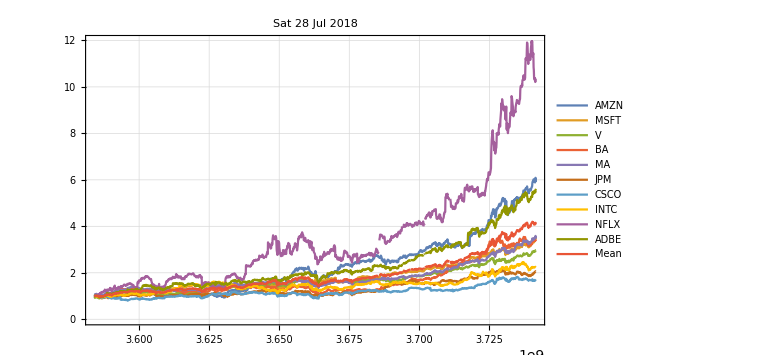
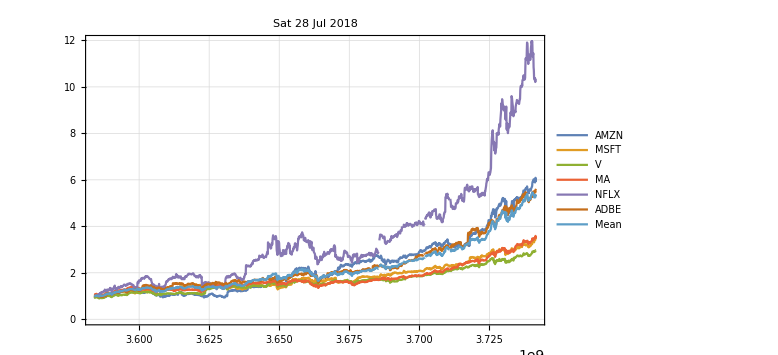
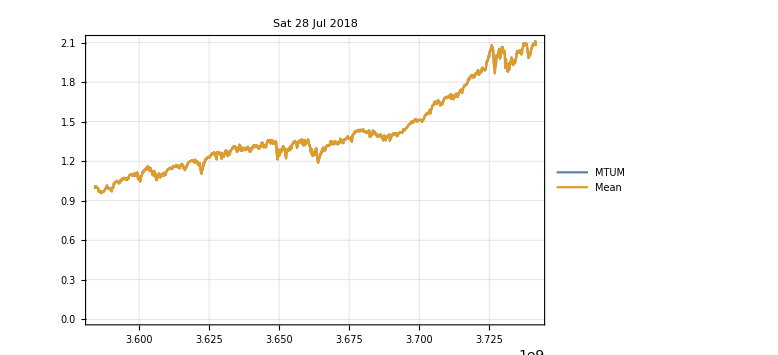
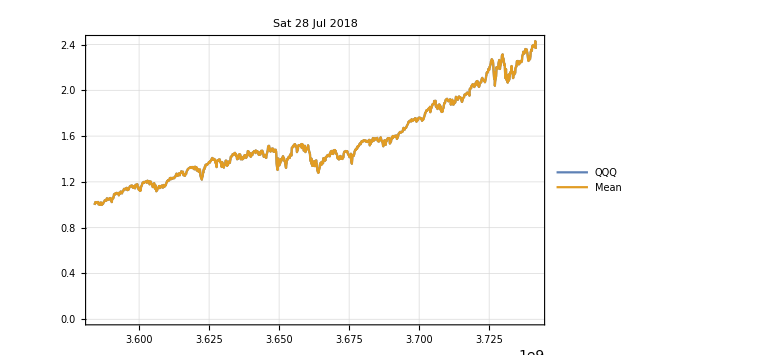
{{-Graphics-,return | 4.12069
std | 0.787244
r/s | 5.23432},{-Graphics-,return | 5.29223
std | 1.06112
r/s | 4.98742},{-Graphics-,return | 2.07344
std | 0.295128
r/s | 7.02557},{-Graphics-,return | 2.36103
std | 0.348834
r/s | 6.76835}}

```mathematica
symbolLists={{"AMZN","MSFT","V","BA","MA","JPM","CSCO","INTC","NFLX","ADBE"},{"AMZN","MSFT","V","MA","NFLX","ADBE"},{"MTUM"},{"QQQ"}};
files={"portfolio10","portfolio6","MTUM","QQQ"};
charts=RobustChart[#,start,end]&/@symbolLists
MapIndexed[Export[FileNameJoin[{NotebookDirectory[],files[[#2]]<>".pdf"}],#1]&,charts];
```

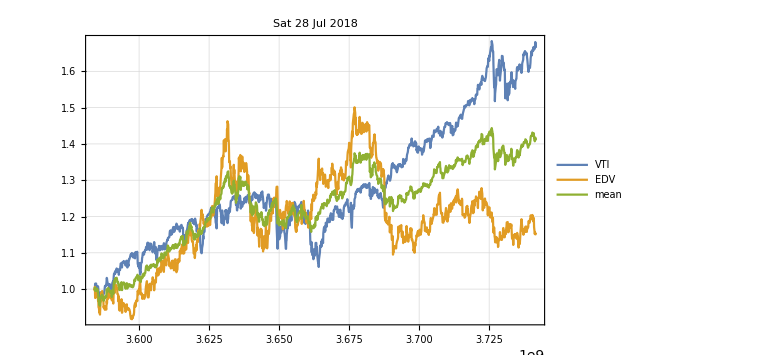
{-Graphics-,return | 1.40959
std | 0.119416
r/s | 11.804}

```mathematica
PortfolioChart[{"VTI","EDV"},start,end]
```

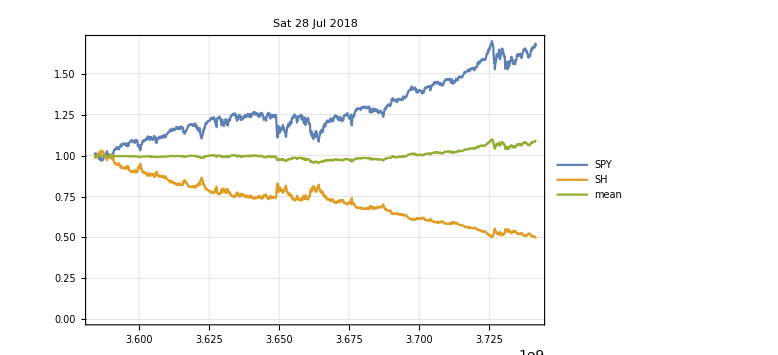
{-Graphics-,return | 1.08623
std | 0.0297337
r/s | 36.5319}

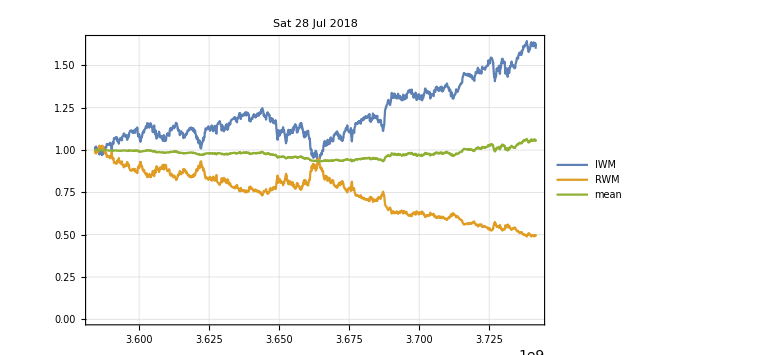
{-Graphics-,return | 1.05005
std | 0.0269165
r/s | 39.0115}

```mathematica
PortfolioChart[{"SPY","SH"},start,end]
PortfolioChart[{"IWM","RWM"},start,end]
```

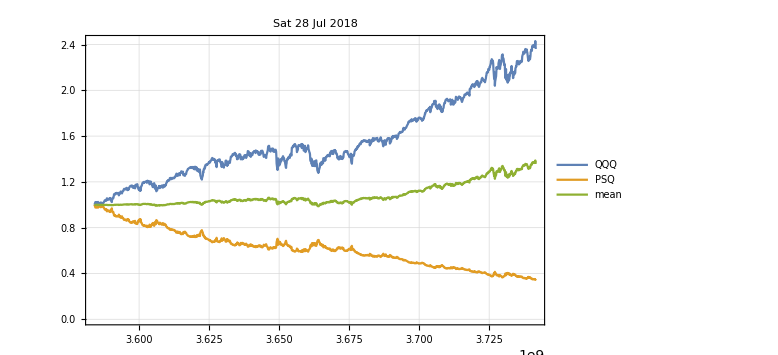
{-Graphics-,return | 1.35735
std | 0.100294
r/s | 13.5336}

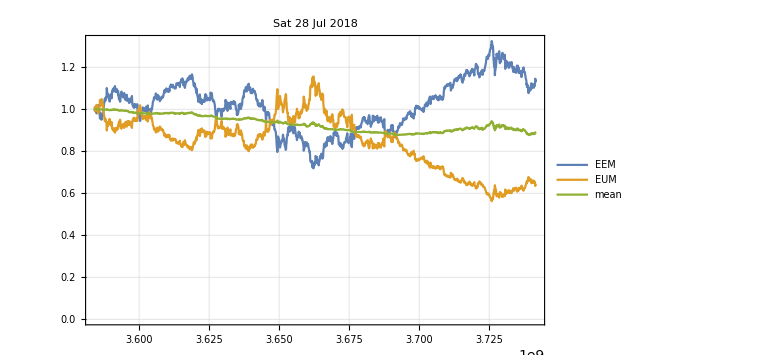
{-Graphics-,return | 0.888086
std | 0.0384401
r/s | 23.1031}

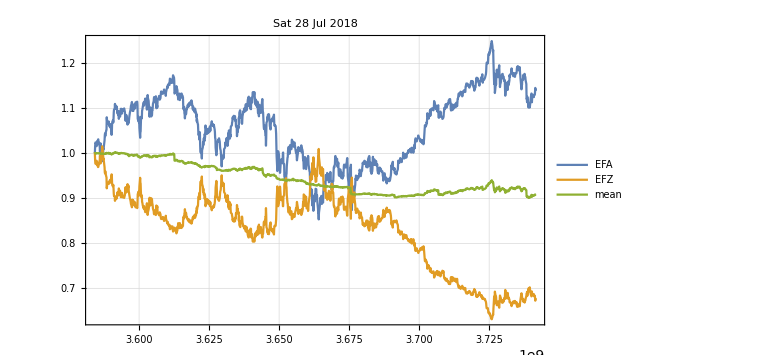
{-Graphics-,return | 0.909123
std | 0.0331784
r/s | 27.4011}

```mathematica
PortfolioChart[{"QQQ","PSQ"},start,end]
PortfolioChart[{"EEM","EUM"},start,end]
PortfolioChart[{"EFA","EFZ"},start,end]
```

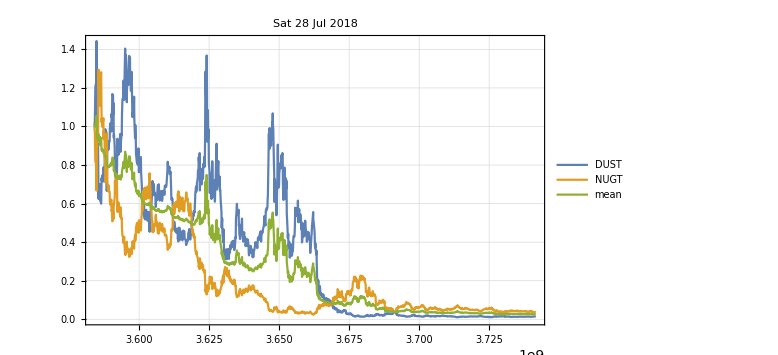
{-Graphics-,return | 0.0247696
std | 0.264988
r/s | 0.0934745}

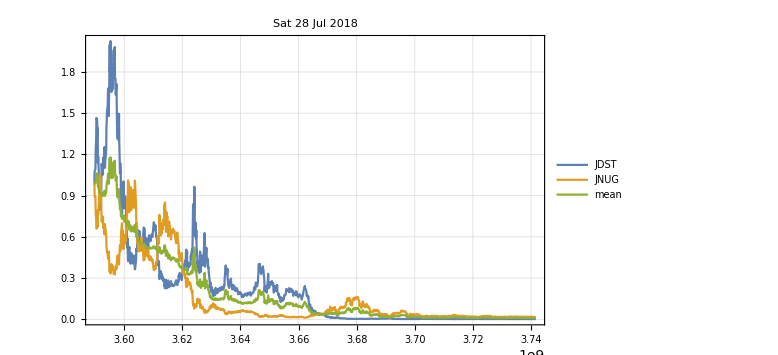
{-Graphics-,return | 0.00874565
std | 0.270416
r/s | 0.0323415}

```mathematica
PortfolioChart[{"DUST","NUGT"},start,end]
PortfolioChart[{"JDST","JNUG"},start,end]
```